## Load package

```mathematica
(* run once to install EcoEvo package v1.7.2 *)PacletInstall["https://github.com/cklausme/EcoEvo/releases/download/1.7.2/EcoEvo-1.7.2.paclet"]
```

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.7.2 (September 1, 2023)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
Charting`$InteractiveHighlighting=False;
```

## Plotting function

```mathematica
Clear[PlotTAD];
PlotTAD[traits_,sol_,opts___?OptionQ]:=
PlotGuild[traits,sol,opts,Logged->True,PlotRange->All,Filling->None,Joined->True,PlotMarkers->None]
```

## Model definition

Note we use T (temperature) as EL, and TR as ER in the main text, respectively

```mathematica
SetModel[{
Guild[Ν]->{Equation:>Subscript[Ν, i](μ[Subscript[Topt, i],T] R-c P-dN)+m (ΝR[Subscript[Topt, i]]-Subscript[Ν, i]),Traits->{Topt},Color->"Rainbow"},
Aux[R]->{Equation:> a(Rin-R)-R Sum[μ[Subscript[Topt, j],T] Subscript[Ν, j],{j,Subscript[𝒩, Ν]}],Color->Blue},
Aux[P]->{Equation:> c P Sum[Subscript[Ν, j],{j,Subscript[𝒩, Ν]}]-dP P,Color->Red},
Parameters:>{Rin≥0,m≥0,μmax>=0,σ>=0,m>=0,dN>=0,T>=0,c>=0, dP>=0,a>=0,ΝRtot>=0,σR>=0,TR}
}];

μ[Topt_,T_]:=μmax E^(-(Topt-T)^2/σ^2);

(* regional trait density distribution *)
nR[Topt_]=ΝRtot/(Sqrt[2 π]σR) E^(-(Topt-TR)^2/(2 σR^2));
```

```mathematica
(* regional trait abundance distribution *)
ΝR[Topt_]=nR[Topt]/z;
```

```mathematica
(* verify that ΝRtot is total regional abundance *)
Integrate[nR[Topt′],{Topt′,-∞,∞}]
```

ΝRtot

## Closed system analytical

```mathematica
(* closed system equilibrium *)
m=0;
eq0=SolveEcoEq[{Subscript[Topt, 1]->T}]
```

{{Ν_1→0,R→Rin,P→0},{Ν_1→(-a dN+a Rin μmax)/(dN μmax),R→dN/μmax,P→0},{Ν_1→dP/c,R→(a c Rin)/(a c+dP μmax),P→(-a c dN-dN dP μmax+a c Rin μmax)/(c (a c+dP μmax))}}

```mathematica
(* closed system invasion rate *)
g0=Inv[{Subscript[Topt, 1]->T},eq0[[-1]]]/.Subscript[Topt, 0]->Topt
```

(a c (-1+ⅇ^(-(T-Topt)^2/σ^2)) Rin μmax)/(a c+dP μmax)

## Parameter values

```mathematica
(* common parameters *)
T=25; (* local temperature *)
dN=0.2; (* consumer death rate *)
σ=7; (* width of environment-response curve *)
μmax=1; (* consumer max growth rate *)
c=0.1; (* predation rate *)
a=0.1; (* resource supply rate *)
dP=0.1; (* predator death rate *)
nsp=401; (* number of species *)
{Toptmin,Toptmax}={0,50};
ρ:=(nsp-1)/(Toptmax-Toptmin); (* species density function *)
z=N@Sum[1/(Sqrt[2 π]σR) E^(-(Topt-TR)^2/(2 σR^2)),{Topt,Toptmin,Toptmax,1/ρ}];(* Normalization constant*)
TR=25; (* average regional env *)
σR=7; (* width of regional TAD *)
```

```mathematica
(* verify ∑ΝR=ΝRtot *)
N@Simplify[Sum[ΝR[Topt],{Topt,Toptmin,Toptmax,1/ρ}]]
```

1. ΝRtot

```mathematica
traits=MakeRuleList[Topt,nsp,{Toptmin,Toptmax}];
```

## Closed system numerical

```mathematica
RinP=Rin/.Solve[(P/.eq0[[-1]])==0,Rin][[1]]
```

2.2

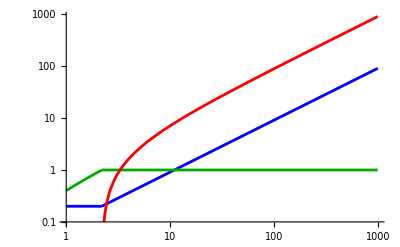

```mathematica
Show[
LogLogPlot[Evaluate[{R,Subscript[Ν, 1],P}/.eq0[[-1]]],{Rin,RinP,1000},PlotRange->{{1,1000},{0.1,All}},PlotStyle->{Blue,Darker@Green,Red}],
LogLogPlot[Evaluate[{R,Subscript[Ν, 1]}/.eq0[[-2]]],{Rin,1,RinP},PlotStyle->{Blue,Darker@Green}]
]
```

## Fig 2: Without predation

```mathematica
ΝRtot=1; (* regional abundance *)
Rin=200;
ics=Join[MakeRuleList[Ν,nsp,0.01],{P->0.,R->0.1}];
```

```mathematica
m=10^-2;
Clear[Rin];
Rin:=10^Rinp;
Dynamic[Rin]
dat=Table[{Rin,FinalSlice[EcoSim[traits,ics,10^8]]},{Rinp,0,2,0.1}];
res=RuleListInterpolation[dat];
```

$Aborted

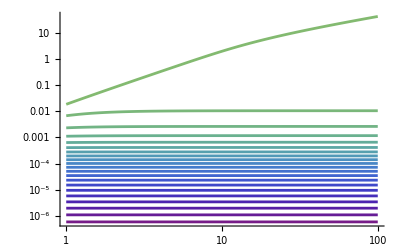

```mathematica
PlotRuleList[res,Table[Subscript[Ν, i],{i,1,201,10}],PlotRange->All,ScalingFunctions->{"Log","Log"}]
```

```mathematica
Rasterize[Show[
PlotRuleList[res,Table[Subscript[Ν, i],{i,101,201,1}],PlotRange->All,ScalingFunctions->{"Log","Log"}],
PlotRuleList[res,Table[Subscript[Ν, i],{i,101,201,10}],PlotStyle->{{Thickness[0.003],Black}},PlotRange->All,ScalingFunctions->{"Log","Log"}],Frame->True,LabelStyle->14],ImageSize->Medium,ImageResolution->500]
```

-Graphics-

```mathematica
Rasterize[Show[
PlotRuleList[res,R,ScalingFunctions->{"Log","Log"},PlotRange->{0.1,All},PlotStyle->Directive[Black,Dashed]],
PlotRuleList[TotalAbundance[res],ScalingFunctions->{"Log","Log"},PlotStyle->Directive[Black]],
Frame->True,LabelStyle->14],ImageSize->Medium,ImageResolution->500]
```

Plot::prng: Value of option PlotRange -> {Automatic,{Automatic,All}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics-

```mathematica
Rasterize[Show[Table[PlotTAD[traits,Slice[res,Rin],PlotStyle->ColorData["BlueGreenYellow",Log10[Rin]/2]],{Rin,{10^2,10,1}}],Frame->True,LabelStyle->14,AxesLabel->None,PlotRange->All],ImageSize->Medium,ImageResolution->500]
```

-Graphics-

```mathematica
Rasterize[Show[Table[PrestonPlot[Slice[res,Rin],ShowSpecies->False,PlotStyle->ColorData["BlueGreenYellow",Log10[Rin]/2]],{Rin,{10^2,10,1}}],PlotRange->{-0.001,All},Frame->True,LabelStyle->14,AxesLabel->None,PlotRange->All],ImageSize->Medium,ImageResolution->500]
```

-Graphics-

#### Legend

```mathematica
Rasterize[LineLegend[Table[ColorData["BlueGreenYellow",Log10[Rin]/2],{Rin,{10^2,10,1}}],{"100","10","1"}],ImageResolution->500]
```

-Graphics-

## Fig 3: With predation

```mathematica
ΝRtot=1; (* regional abundance *)
ics=Join[MakeRuleList[Ν,nsp,0.01],{P->0.1,R->0.1}];
```

```mathematica
m=10^-2;
Clear[Rin];
Rin:=10^Rinp;
Dynamic[Rin]
dat=Table[{Rin,FinalSlice[EcoSim[traits,ics,10^8]]},{Rinp,0,2,0.02}];
res=RuleListInterpolation[dat];
```

$Aborted

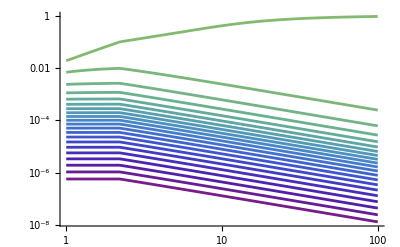

```mathematica
PlotRuleList[res,Table[Subscript[Ν, i],{i,1,201,10}],PlotRange->All,ScalingFunctions->{"Log","Log"}]
```

```mathematica
Rasterize[Show[
PlotRuleList[res,Table[Subscript[Ν, i],{i,101,201,1}],PlotRange->All,ScalingFunctions->{"Log","Log"}],
PlotRuleList[res,Table[Subscript[Ν, i],{i,101,201,10}],PlotStyle->{{Thickness[0.003],Black}},PlotRange->All,ScalingFunctions->{"Log","Log"}],LabelStyle->14,GridLines->{{.75},None},GridLinesStyle->Directive[Black,Dashed],Frame->True],ImageSize->Medium,ImageResolution->500]
```

-Graphics-

```mathematica
Rasterize[Show[
PlotRuleList[res,{R,P},ScalingFunctions->{"Log","Log"},PlotRange->{0.1,All},PlotStyle->{Directive[Black,Dashed],Cyan}],
PlotRuleList[TotalAbundance[res],ScalingFunctions->{"Log","Log"},PlotRange->{0.1,All},PlotStyle->Directive[Black]],Frame->True,LabelStyle->14],ImageSize->Medium,ImageResolution->500]
```

-Graphics-

```mathematica
Rasterize[Show[Table[PlotTAD[traits,Slice[res,Rin],PlotStyle->ColorData["BlueGreenYellow",Log10[Rin]/2]],{Rin,{10^2,10,1}}],Frame->True,LabelStyle->14,AxesLabel->None,PlotRange->All],ImageSize->Medium,ImageResolution->500]
```

-Graphics-

```mathematica
Rasterize[Show[Table[PrestonPlot[Slice[res,Rin],ShowSpecies->False,PlotStyle->ColorData["BlueGreenYellow",Log10[Rin]/2]],{Rin,{10^2,10^1,1}}],PlotRange->{-0.001,All},Frame->True,LabelStyle->14,AxesLabel->None,PlotRange->All],ImageSize->Medium,ImageResolution->500]
```

-Graphics-

## Fig. 4: Varying local environment

#### Common parameters

```mathematica
T=15; (* local environment *)
dN=0.1; (* consumer death rate *)
σ=6; (* width of env-response curve *)
μmax=1; (* consumer max growth rate *)
c=0.1; (* predator consumption rate *)
a=0.1; (* resource supply rate *)
dP=0.1; (* predator death rate *)
nsp=101; (* number of species *)
{Toptmin,Toptmax}={0,50};
ρ:=(nsp-1)/(Toptmax-Toptmin); (* species density function *)
TR=20; (* average regional env *)
σR=1; 
ΝRtot=10; (* regional abundance *)
traits=MakeRuleList[Topt,nsp,{10,30}];
ics=Join[MakeRuleList[Ν,nsp,0.01],{P->0.1,R->0.1}];
```

#### m=10^-1

```mathematica
m=10^-1;
T=15;
TR=20;
Rin=5;
Rasterize[ListPlot[sol=EcoSim[traits,ics,10^6,NDSolveOpts->{AccuracyGoal->128}];Transpose[{Values[traits],Table[Subscript[Ν, i],{i,1,nsp}]/.FinalSlice[sol]}],Joined->True,PlotRange->{{10,30},All},Frame->True,FrameLabel->None,AspectRatio->.75,FrameTicks->{{Automatic,None},{{10,25,30,{T,"E_L"},{TR,"E_R"}},None}},FrameTicksStyle->15,GridLines->{{T,TR},None},GridLinesStyle->Directive[Black,Dashed],PlotStyle->Black],ImageResolution->500]
```

-Graphics-

```mathematica
dat= Table[T=i;
Table[Subscript[Ν, i],{i,1,nsp}]/.FinalSlice[EcoSim[traits,ics,10^6,NDSolveOpts->{AccuracyGoal->128}]],{i,10,30,0.2}];
datnorm=dat/Max[dat];
Rasterize[ArrayPlot[Reverse@Transpose@dat,Frame->{{True,None},{True,None}},FrameTicks->{{{10,15,25,30,{TR,"E_R"}},None},{Automatic,None}},LabelStyle->18,DataReversed->False,DataRange->{{10,30},{10,30}},AspectRatio->0.75,GridLines->{{15},None},GridLinesStyle->Directive[Red,Dashed,Thickness[0.003]]],ImageResolution->500,ImageSize->Medium]
```

-Graphics-

#### m=10^-2 (bi-modality)

```mathematica
m=10^-2;
T=15;
TR=20;
Rasterize[ListPlot[Table[Rin=p;
sol=EcoSim[traits,ics,10^8,NDSolveOpts->{AccuracyGoal->128}];Transpose[{Values[traits],Table[Subscript[Ν, i],{i,1,nsp}]/.FinalSlice[sol]}],{p,1,2,0.5}],Joined->True,PlotStyle->Table[ColorData["BlueGreenYellow",(Rin-1)/1],{Rin,1,2,0.5}],PlotRange->{{10,30},All},Frame->True,FrameLabel->None,AspectRatio->.75,FrameTicks->{{Automatic,None},{{10,25,30,{T,"E_L"},{TR,"E_R"}},None}},FrameTicksStyle->15,GridLines->{{T,TR},None},GridLinesStyle->Directive[Black,Dashed]],ImageResolution->500]
```

-Graphics-

```mathematica
Rasterize[LineLegend[Table[ColorData["BlueGreenYellow",(Rin-1)/1],{Rin,1,2,0.5}],{"2","1.5","1"}],ImageResolution->500]
```

-Graphics-

```mathematica
dat= Table[T=i;
Table[Subscript[Ν, i],{i,1,nsp}]/.FinalSlice[EcoSim[traits,ics,10^6,NDSolveOpts->{AccuracyGoal->128}]],{i,10,30,0.2}];
datnorm=dat/Max[dat];
Rasterize[ArrayPlot[Reverse@Transpose@dat,Frame->{{True,None},{True,None}},FrameTicks->{{{10,15,25,30,{TR,"E_R"}},None},{Automatic,None}},LabelStyle->18,DataReversed->False,DataRange->{{10,30},{10,30}},AspectRatio->0.75,GridLines->{{15},None},GridLinesStyle->Directive[Red,Dashed,Thickness[0.003]]],ImageResolution->500,ImageSize->Medium]
```

-Graphics-

#### m=10^-3

```mathematica
m=10^-3;
T=15;
TR=20;
Rin=5;
Rasterize[ListPlot[sol=EcoSim[traits,ics,10^6,NDSolveOpts->{AccuracyGoal->128}];Transpose[{Values[traits],Table[Subscript[Ν, i],{i,1,nsp}]/.FinalSlice[sol]}],Joined->True,PlotRange->{{10,30},All},Frame->True,FrameLabel->None,AspectRatio->.75,FrameTicks->{{Automatic,None},{{10,25,30,{T,"E_L"},{TR,"E_R"}},None}},FrameTicksStyle->15,GridLines->{{T,TR},None},GridLinesStyle->Directive[Black,Dashed],PlotStyle->Black],ImageResolution->500]
```

-Graphics-

```mathematica
dat= Table[T=i;
Table[Subscript[Ν, i],{i,1,nsp}]/.FinalSlice[EcoSim[traits,ics,10^6,NDSolveOpts->{AccuracyGoal->128}]],{i,10,30,0.2}];
datnorm=dat/Max[dat];
Rasterize[ArrayPlot[Reverse@Transpose@dat,Frame->{{True,None},{True,None}},FrameTicks->{{{10,15,25,30,{TR,"E_R"}},None},{Automatic,None}},LabelStyle->18,DataReversed->False,DataRange->{{10,30},{10,30}},AspectRatio->0.75,GridLines->{{15},None},GridLinesStyle->Directive[Red,Dashed,Thickness[0.003]]],ImageResolution->500,ImageSize->Medium]
```

-Graphics-

## Supplement S1: Approximations

#### Common parameters

```mathematica
T=25; (* local temperature *)
dN=0.2; (* consumer death rate *)
σ=7; (* width of environment-response curve *)
μmax=1; (* consumer max growth rate *)
c=0.1; (* predation rate *)
a=0.1; (* resource supply rate *)
dP=0.1; (* predator death rate *)
nsp=401; (* number of species *)
{Toptmin,Toptmax}={0,50};
ρ:=(nsp-1)/(Toptmax-Toptmin); (* species density function *)
z=N@Sum[1/(Sqrt[2 π]σR) E^(-(Topt-TR)^2/(2 σR^2)),{Topt,Toptmin,Toptmax,1/ρ}];(* Normalization constant*)
TR=25; (* average regional temperature *)
σR=7;
```

#### With predation

```mathematica
Ν0:=dP/c;
R0:=a Rin/(a+μmax Ν0);
Γ0:=π m nR[T] *σ^2/(μmax R0 Ν0); (* Eq. S25 *)
z=N@Sum[1/(Sqrt[2 π]σR) E^(-(Topt-TR)^2/(2 σR^2)),{Topt,Toptmin,Toptmax,1/ρ}];(* Normalization constant*)
T=TR=25;
σR=σ;
napprox[Topt_]:=m nR[Topt]/((μmax-μ[Topt,T]+μmax Γ0^2/σ^2)R0); (* Eq. S22 *)
(* simple n-to-Ν conversion *)
Νapprox[Topt_]:=napprox[Topt]/ρ;
```

```mathematica
ΝRtot=1;
m=10^-2;
Rin=10;
nsp=401;
traits=MakeRuleList[Topt,nsp,{0,50}];
ics=Join[MakeRuleList[Ν,nsp,0.01],{P->0.1,R->0.1}];
sol=FinalSlice[EcoSim[traits,ics,10^8]];
```

```mathematica
Rasterize[GraphicsRow[{
Show[
LogPlot[{Νapprox[Topt]},{Topt,0,50},PlotRange->All],
PlotTAD[traits,sol,Joined->False,PlotStyle->Black,PlotMarkers->{Automatic,4}]
],
Show[
LogPlot[{Νapprox[Topt]},{Topt,22,28},PlotRange->All],
PlotTAD[traits,sol,Joined->False,PlotStyle->Black,PlotMarkers->{Automatic,7}],
PlotRange->{{22,28},{-7.85,1}}]
},ImageSize->Large, Spacings->10],ImageResolution->500]
```

-Graphics-

#### No predation

```mathematica
R0:=dN/(μmax);
Ν0:=a*(Rin-R0)/(μmax*R0);
Γ0:=π m nR[T]σ^2/(μmax R0 Ν0); (* Eq. S15 *)
σR=σ=σ;
TR=T;
napprox[Topt_]:=m nR[Topt]/((μmax-μ[Topt,T]+μmax Γ0^2/σ^2)R0);
```

```mathematica
(* simple n-to-Ν conversion *)
Νapprox[Topt_]:=napprox[Topt]/ρ;
```

```mathematica
ΝRtot=1;
m=10^-2;
Rin=10;
ics=Join[MakeRuleList[Ν,nsp,0.01],{P->0.,R->0.1}];
sol=FinalSlice[EcoSim[traits,ics,10^8]];

Rasterize[
GraphicsRow[{
Show[
LogPlot[{Νapprox[Topt]},{Topt,0,50},PlotRange->All],
PlotTAD[traits,sol,Joined->False,PlotStyle->Black,PlotMarkers->{Automatic,4}]
],
Show[
LogPlot[{Νapprox[Topt]},{Topt,24,26.05},PlotRange->All],
PlotTAD[traits,sol,Joined->False,PlotStyle->Black,PlotMarkers->{Automatic,7}],
PlotRange->{{24,26.05},{-4.45,1}}
]
}, Spacings->10],ImageResolution->500]
```

-Graphics-

## Appendix A: Evenness

#### Evenness

```mathematica
evenness[list_]:=1/Length[list]*Exp[-Total@Table[i*Log[i],{i,list/Total[list]}]];
```

```mathematica
m=10^-2;
T=TR=25; (* local temperature *)
σ=σR=7;
dN=0.2; (* phyto death rate *)
c=0.3;
μmax=1; (* phyto max growth rate *)
a=0.5; (* resource supply rate *)
dP=0.1; (* zooplankton death rate *)
{Toptmin,Toptmax}={0,30};
ρ:=(nsp-1)/(Toptmax-Toptmin); (* species density function *)
nsp=200; (* number of species *)
ΝRtot=1;
traits=MakeRuleList[Topt,nsp,{Toptmin,Toptmax}];(* regional abundance *)
```

```mathematica
Rmin=-1.5;
Rmax=2;
step=0.1;
ics=Join[MakeRuleList[Ν,nsp,0.01],{P->0.1,R->0.1}];
wp=
Table[Rin=10^i;
sad=Table[Subscript[Ν, i],{i,1,nsp}]/.FinalSlice[EcoSim[traits,ics,10^8]];{Rin,evenness[sad]},{i,Rmin,Rmax,step}];
```

```mathematica
ics=Join[MakeRuleList[Ν,nsp,0.01],{P->0.,R->0.1}];
wop=
Table[Rin=10^i;
sad=Table[Subscript[Ν, i],{i,1,nsp}]/.FinalSlice[EcoSim[traits,ics,10^8]];{Rin,evenness[sad]},{i,Rmin,Rmax,step}];
```

```mathematica
Rasterize[Show[{ListPlot[wop,PlotStyle->Black,Joined->True,ScalingFunctions->{"Log",None}],ListPlot[wp,PlotStyle->Directive[Black,Dashed],Joined->True,ScalingFunctions->{"Log",None}]},PlotRange->{All,All},LabelStyle->14],ImageSize->Large,ImageResolution->500]
```

-Graphics-